## Assymmetric Molecule: Dispersion

```mathematica
ClearAll[J,ω0,ω1,ω2,ω3,Ω]
Ω[μ_]:=({{ω1[μ], -J, 0}, {-J, ω2[μ], -J}, {0, -J, ω3[μ]}});
```

```mathematica
ω1[μ_]:=ω0 +d1×μ + d2/2 μ^2;
ω2[μ_]:=ω0 +D1×(2μ) + D2/2(2μ)^2;
ω3[μ_]:=ω0+d1×μ + d2/2 μ^2 ;
```

```mathematica
d1 = 400;
D1 = d1/2;
d2 =-0.015;
D2 = 0.010;
ω0 = 0;
J =3;
```

```mathematica
freqs= Sort[Eigenvalues[Ω[μ]]];
ωS=freqs[[1]];
ωC=freqs[[2]];
ωAS=freqs[[3]];
```

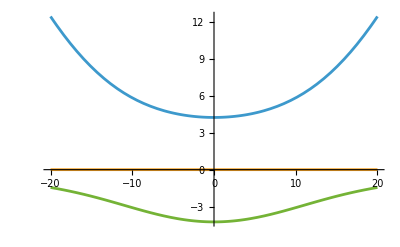

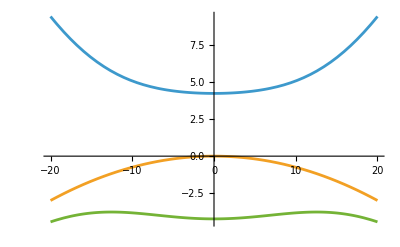

```mathematica
Plot[{ωAS-ωC,ωC-ωC,ωS-ωC}, {μ,-20,20}]
Plot[{ωAS-(d1×μ),ωC-(d1×μ),ωS-(d1×μ)}, {μ,-20,20}]
```